# Assembly Theory : Combinatorial Spaces of Peptides

THIS NOTEBOOK REQUIRES READING LARGE DATAFILES WHICH ARE NOT AVAILABLE ON GITHUB . THE ASSEMBLY CALCULATIONS FILES CAN BE AVAILAVLE ON A REASONABLE REQUEST FROM THE CORRESPONDING AUTHOR .

## Combinatorial Assembly Spaces of strings

In this section, we calculate the assembly index of binary, ternary, and quaternary strings up to length 16 (14 for quaternary strings due to large number of possible strings) which represents the growth of assembly universe for strings. It requires enumerating all the strings up to length 16 for complete quantification up to assembly index 4. This gives an idea about how fast the combinatorial space grows vs. assembly index with different number of unique building blocks, which is particularly important for the experiments. The assembly indices of all the strings were calculated using assemblyCpp code. (https://arxiv.org/abs/2410.09100)

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/

```mathematica
totalStrings[k_,n_]:=k(k^n-1)/(k-1)
```

```mathematica
binaryStringList=Flatten@ParallelTable[StringSplit[Import[baseDirectory<>"combinatorial_strings/binary_strings/BinaryStringsList_"<>ToString[i]<>".txt","Text"],"\n"],{i,16}];
```

```mathematica
binaryStringAssemblyList=Flatten@ParallelTable[ToExpression@StringSplit[Import[baseDirectory<>"combinatorial_strings/binary_strings/BinaryStringsList_"<>ToString[i]<>".txtOut","Text"],"\n"],{i,16}];
```

```mathematica
Length@binaryStringList
```

131070

```mathematica
Length@binaryStringAssemblyList
```

131070

```mathematica
totalStrings[2,16]
```

131070

```mathematica
binList2=Tally@binaryStringAssemblyList;
```

```mathematica
Export[baseDirectory<>"binList_2.csv",binList2,"CSV"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/binList_2.csv

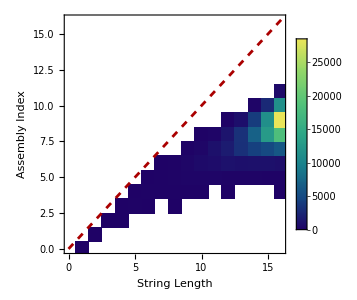

```mathematica
Show[{DensityHistogram[MapThread[{#1,#2}&,{StringLength/@binaryStringList,binaryStringAssemblyList}],16, ChartLegends->Automatic,AspectRatio->1,ColorFunction->"BlueGreenYellow",PlotRange->{{0,16},{0,16}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"String Length","Assembly Index"}],Plot[x,{x,0,16},PlotStyle->{Darker@Red,Dashed},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True]},ImageSize->300]
```

```mathematica
ternaryStringList=Flatten@ParallelTable[StringSplit[Import[baseDirectory<>"combinatorial_strings/ternary_strings/TernaryStringsList_"<>ToString[i]<>".txt","Text"],"\n"],{i,16}];
```

```mathematica
ternaryStringAssemblyList=Flatten@ParallelTable[ToExpression@StringSplit[Import[baseDirectory<>"combinatorial_strings/ternary_strings/TernaryStringsList_"<>ToString[i]<>".txtOut","Text"],"\n"],{i,16}];
```

```mathematica
Length@ternaryStringList
```

64570080

```mathematica
Length@ternaryStringAssemblyList
```

64570080

```mathematica
totalStrings[3,16]
```

64570080

```mathematica
binList3=Tally@ternaryStringAssemblyList;
```

```mathematica
Export[baseDirectory<>"binList_3.csv",binList3,"CSV"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/binList_3.csv

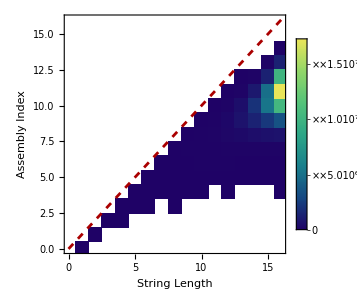

```mathematica
Show[{DensityHistogram[MapThread[{#1,#2}&,{StringLength/@ternaryStringList,ternaryStringAssemblyList}],16, ChartLegends->Automatic,AspectRatio->1,ColorFunction->"BlueGreenYellow",PlotRange->{{0,16},{0,16}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"String Length","Assembly Index"}],Plot[x,{x,0,16},PlotStyle->{Darker@Red,Dashed},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True]},ImageSize->300]
```

```mathematica
quaternaryStringList=Flatten@ParallelTable[StringSplit[Import[baseDirectory<>"combinatorial_strings/quaternary_strings/QuaternaryStringsList_"<>ToString[i]<>".txt","Text"],"\n"],{i,15}];
```

```mathematica
quaternaryStringAssemblyList=Flatten@ParallelTable[ToExpression@StringSplit[Import[baseDirectory<>"combinatorial_strings/quaternary_strings/QuaternaryStringsList_"<>ToString[i]<>".txtOut","Text"],"\n"],{i,15}];
```

```mathematica
Length@quaternaryStringList
```

1431655764

```mathematica
Length@quaternaryStringAssemblyList
```

1431655764

```mathematica
totalStrings[4,15]
```

1431655764

```mathematica
binList4=Tally@quaternaryStringAssemblyList;
```

```mathematica
Export[baseDirectory<>"binList_4.csv",binList4,"CSV"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/binList_4.csv

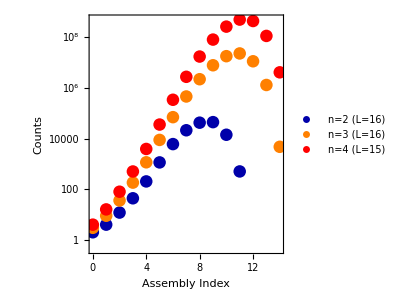

```mathematica
plot1=ListLogPlot[{binList2,binList3,binList4},FrameTicks->{{All,None},{All,None}},PlotStyle->{{Darker@Blue,PointSize[0.03]},{Orange,PointSize[0.03]},{Red,PointSize[0.03]}},AspectRatio->1,Frame->True,FrameLabel->{"Assembly Index","Counts"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},PlotLegends->Placed[PointLegend[{"n=2 (L=16)","n=3 (L=16)","n=4 (L=15)"},Spacings->0.3],{0.25,0.85}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"AssemblyDistribution.png",plot1,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/AssemblyDistribution.png

```mathematica
Export[baseDirectory<>"AssemblyDistribution.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/AssemblyDistribution.svg

## Generating Assembly Space from an undirected process

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/

```mathematica
SeedRandom[111]
```

RandomGeneratorState[…]

Here, we generate assembly possible by random combination (undirected) of objects within a physical space. We investigate the expansion of assembly space with different number of initial objects and comparing the shared spaces different exploration runs.

```mathematica
generateAssemblyPossible[nInitObjects_,nSteps_]:=Module[{initObjects,obj1,obj2},
Clear[assemblyPool,assemblyStep];
initObjects=Alphabet[][[1;;nInitObjects]];
assemblyPool=initObjects;assemblyStep={};
Monitor[Table[
obj1=RandomChoice[assemblyPool];(* Selecting first object randomly *)
obj2=RandomChoice[assemblyPool];(* Selecting second object randomly *)
assemblyStep=Union@Append[assemblyStep,{obj1->obj1<>obj2,obj2->obj1<>obj2}];
assemblyPool=Union@Append[assemblyPool,obj1<>obj2],{i,1,nSteps}],i]; Return[{assemblyStep,assemblyPool}]]
```

```mathematica
p0=generateAssemblyPossible[5,50];graphp0=Graph[Flatten@p0[[1]]];objectListp0=p0[[2]];
```

```mathematica
p1=generateAssemblyPossible[5,10^2];graphp1=Graph[Flatten@p1[[1]]];objectListp1=p1[[2]];
```

```mathematica
p2=generateAssemblyPossible[5,10^3];graphp2=Graph[Flatten@p2[[1]]];objectListp2=p2[[2]];
```

```mathematica
p3=generateAssemblyPossible[5,10^4];graphp3=Graph[Flatten@p3[[1]]];objectListp3=p3[[2]];
```

```mathematica
Export[baseDirectory<>"objectList_50.txt",objectListp0,"Text"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/objectList_50.txt

```mathematica
Export[baseDirectory<>"objectList_100.txt",objectListp1,"Text"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/objectList_100.txt

```mathematica
Export[baseDirectory<>"objectList_1000.txt",objectListp2,"Text"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/objectList_1000.txt

```mathematica
Export[baseDirectory<>"objectList_10000.txt",objectListp3,"Text"]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/objectList_10000.txt

```mathematica
stringSel=Block[{len=StringLength@objectListp0,pos},pos=First@Flatten@Position[len,Max@len];objectListp0[[pos]]];
```

```mathematica
graphSelected=VertexInComponentGraph[graphp0,{stringSel}];
```

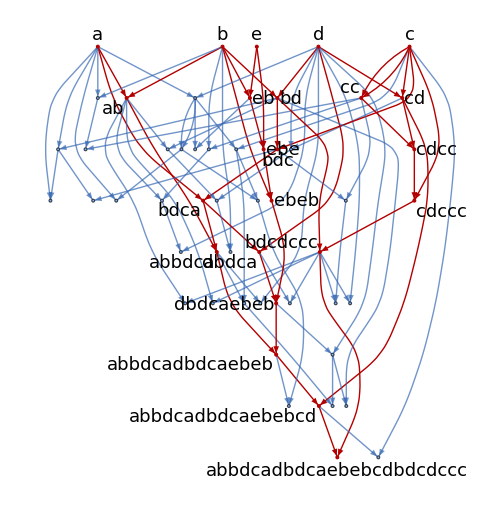

```mathematica
plot1=HighlightGraph[graphp0,graphSelected,GraphLayout->{"LayeredDigraphEmbedding", "RootVertex"->{"a","b","c","d","e"}},VertexLabels->Evaluate[(#->Style[#,Background->LightGreen])&/@VertexList@graphSelected],VertexLabelStyle->Directive[Black,18],AspectRatio->1.0,ImageSize->500]
```

```mathematica
Export[baseDirectory<>"physical_path_example.png",plot1,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/physical_path_example.png

```mathematica
Export[baseDirectory<>"physical_path_example.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/physical_path_example.svg

```mathematica
CreateDirectory[baseDirectory<>"p1"];
Table[Export[baseDirectory<>"p1/objectListp1_"<>ToString[i]<>".txt",objectListp1[[i]]],{i,Length@objectListp1}];
```

```mathematica
CreateDirectory[baseDirectory<>"p2"];
Table[Export[baseDirectory<>"p2/objectListp2_"<>ToString[i]<>".txt",objectListp2[[i]]],{i,Length@objectListp2}];
```

```mathematica
CreateDirectory[baseDirectory<>"p3"];
Table[Export[baseDirectory<>"p3/objectListp3_"<>ToString[i]<>".txt",objectListp3[[i]]],{i,Length@objectListp3}];
```

```mathematica
pathwayLengthp1=1/2 Length@EdgeList@(VertexInComponentGraph[graphp1,#])&/@objectListp1;
```

```mathematica
pathwayLengthp2=1/2 Length@EdgeList@(VertexInComponentGraph[graphp2,#])&/@objectListp2;
```

```mathematica
pathwayLengthp3=1/2 Length@EdgeList@(VertexInComponentGraph[graphp3,#])&/@objectListp3;
```

```mathematica
plot2= Histogram[{pathwayLengthp3,pathwayLengthp2,pathwayLengthp1},250,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->17]},Frame->True,FrameLabel->{"Pathway Length","Unique Objects"},ChartLegends->Placed[{"10^4 steps","10^3 steps","10^2 steps"},{0.8,0.8}],ChartStyle->3,ImageSize->400];
```

```mathematica
plot3=Histogram[{pathwayLengthp3,pathwayLengthp2,pathwayLengthp1},250,AspectRatio->1,ScalingFunctions->"Log",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->17]},Frame->True,FrameLabel->{"Pathway Length","Unique Objects"},ChartLegends->Placed[{"10^4 steps","10^3 steps","10^2 steps"},{0.8,0.8}],ChartStyle->3,ImageSize->400];
```

```mathematica
GraphicsRow[{plot2,plot3},ImageSize->800];
```

```mathematica
objectListp1=Flatten@Import[baseDirectory<>"objectList_100.txt","Data"];
```

```mathematica
objectListp2=Flatten@Import[baseDirectory<>"objectList_1000.txt","Data"];
```

```mathematica
objectListp3=Flatten@Import[baseDirectory<>"objectList_10000.txt","Data"];
```

THIS SECTION REQUIRES READING LARGE DATAFILES WHICH ARE NOT AVAILABLE ON GITHUB . THE ASSEMBLY CALCULATIONS FILES CAN BE AVAILAVLE ON A REASONABLE REQUEST FROM THE CORRESPONDING AUTHOR.
THE ASSEMBLY CALCULATIONS WERE PERFORMED INDEPENDENTLY, AND THE READ THROUGH THE CODE TO CREATE THE FIGURES BELOW.

```mathematica
dataTmp=Table[Import[baseDirectory<>"p1/objectListp1_"<>ToString[i]<>".txtOut"],{i,Length@objectListp1}];
assemblyIndicesP1=Table[Block[{dat=StringSplit[StringSplit[dataTmp[[i]],"\n"][[1]]," "]},{First@dat,ToExpression@Last@dat}],{i,Length@dataTmp}];
```

```mathematica
dataTmp=Table[Import[baseDirectory<>"p2/objectListp2_"<>ToString[i]<>".txtOut"],{i,Length@objectListp2}];
assemblyIndicesP2=Table[Block[{dat=StringSplit[StringSplit[dataTmp[[i]],"\n"][[1]]," "]},{First@dat,ToExpression@Last@dat}],{i,Length@dataTmp}];
```

```mathematica
dataTmp=Table[Import[baseDirectory<>"p3/objectListp3_"<>ToString[i]<>".txtOut"],{i,Length@objectListp3}];
assemblyIndicesP3=Table[Block[{dat=StringSplit[StringSplit[dataTmp[[i]],"\n"][[1]]," "]},{First@dat,ToExpression@Last@dat}],{i,Length@dataTmp}];
```

```mathematica
plot4=Histogram[{assemblyIndicesP3[[All,2]],assemblyIndicesP2[[All,2]],assemblyIndicesP1[[All,2]]},250,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->26]},Frame->True,FrameLabel->{"Assembly Index","Unique Objects"},ChartLegends->Placed[{"10^4 steps","10^3 steps","10^2 steps"},{0.8,0.8}],ChartStyle->3,ImageSize->400];
```

```mathematica
plot5=Histogram[{assemblyIndicesP3[[All,2]],assemblyIndicesP2[[All,2]],assemblyIndicesP1[[All,2]]},250,AspectRatio->1,ScalingFunctions->"Log",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->26]},Frame->True,FrameLabel->{"Assembly Index","Unique Objects"},ChartLegends->Placed[{"10^4 steps","10^3 steps","10^2 steps"},{0.8,0.8}],ChartStyle->3,ImageSize->400];
```

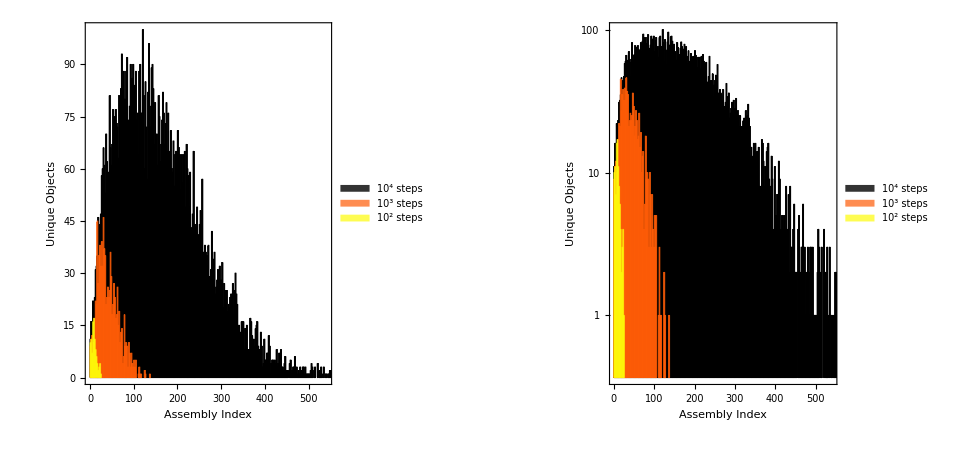

```mathematica
GraphicsRow[{plot4,plot5},ImageSize->800]
```

```mathematica
Export[baseDirectory<>"PathlengthDistribution.png",plot2,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/PathlengthDistribution.png

```mathematica
Export[baseDirectory<>"PathlengthDistribution.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/PathlengthDistribution.svg

```mathematica
Export[baseDirectory<>"AssemblyIndexDistribution.png",plot4,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/AssemblyIndexDistribution.png

```mathematica
Export[baseDirectory<>"AssemblyIndexDistribution.svg",plot4]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/AssemblyIndexDistribution.svg

```mathematica
nRuns=25; (* Total number of runs *)
```

```mathematica
(* Rewriting the function for parallel table, removing the monitor function as used previously *)
generateAssemblyPossible[nInitObjects_,nSteps_]:=Module[{initObjects,obj1,obj2},
Clear[assemblyPool,assemblyStep];
initObjects=Alphabet[][[1;;nInitObjects]];
assemblyPool=initObjects;assemblyStep={};
Table[
obj1=RandomChoice[assemblyPool];(* Selecting first object randomly *)
obj2=RandomChoice[assemblyPool];(* Selecting second object randomly *)
assemblyStep=Union@Append[assemblyStep,{obj1->obj1<>obj2,obj2->obj1<>obj2}];
assemblyPool=Union@Append[assemblyPool,obj1<>obj2],{i,1,nSteps}]; Return[{assemblyStep,assemblyPool}]]
```

```mathematica
p0=ParallelTable[generateAssemblyPossible[5,50],{i,nRuns}];
p1=ParallelTable[generateAssemblyPossible[5,10^2],{i,nRuns}];
p2=ParallelTable[generateAssemblyPossible[5,10^3],{i,nRuns}];
p3=ParallelTable[generateAssemblyPossible[5,10^4],{i,nRuns}];
```

```mathematica
Dimensions/@{p0,p1,p2,p3}
```

{{25,2},{25,2},{25,2},{25,2}}

Getting the list of graph objects and object list

```mathematica
graphp0List=Table[Graph[Flatten@p0[[i]][[1]]],{i,nRuns}]; 
graphp1List=Table[Graph[Flatten@p1[[i]][[1]]],{i,nRuns}]; 
graphp2List=Table[Graph[Flatten@p2[[i]][[1]]],{i,nRuns}]; 
graphp3List=Table[Graph[Flatten@p3[[i]][[1]]],{i,nRuns}];
```

```mathematica
objectListp0=Table[p0[[i]][[2]],{i,nRuns}];
objectListp1=Table[p1[[i]][[2]],{i,nRuns}];
objectListp2=Table[p2[[i]][[2]],{i,nRuns}];
objectListp3=Table[p3[[i]][[2]],{i,nRuns}];
```

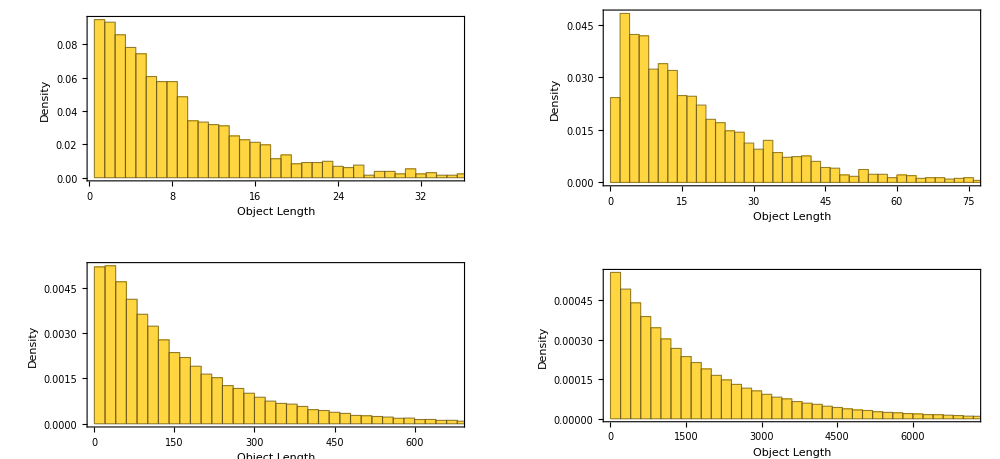

```mathematica
GraphicsGrid[Partition[{Histogram[Flatten@Table[StringLength/@objectListp0[[i]],{i,nRuns}],100,"PDF",AspectRatio->1/3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"Object Length","Density"},ImageSize->300],
Histogram[Flatten@Table[StringLength/@objectListp1[[i]],{i,nRuns}],100,"PDF",AspectRatio->1/3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"Object Length","Density"},ImageSize->300],
Histogram[Flatten@Table[StringLength/@objectListp2[[i]],{i,nRuns}],100,"PDF",AspectRatio->1/3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"Object Length","Density"},ImageSize->300],
Histogram[Flatten@Table[StringLength/@objectListp3[[i]],{i,nRuns}],100,"PDF",AspectRatio->1/3,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"Object Length","Density"},ImageSize->300]},2],ImageSize->1000]
```

## Generating Assembly Space as an undirected process weighted by copy number at different selective factors

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/

TO RUN SIMULATION

```mathematica
(* This function takes very long time to run : Approx 24-36 hours *)
runSimulation[selectiveFactor_,baseDirectory_,nRuns_:16,nSteps_:10^6,initPop_:10^6,baseSeed_:123]:=Module[{simDir,dataSimOut},simDir=FileNameJoin[{baseDirectory,"SelectiveFac_"<>ToString[selectiveFactor]}];
If[DirectoryQ[simDir],DeleteDirectory[simDir,DeleteContents->True]];
CreateDirectory[simDir,CreateIntermediateDirectories->True];
Do[CreateDirectory[FileNameJoin[{simDir,"string_data_"<>ToString[i]}]],{i,nRuns}];
dataSimOut=ParallelTable[Block[{seqList,popList,endsList,boostMask,posActive,p,w,s,obj1,obj2,i1,object,posA,posB,posN,step=0},SeedRandom[baseSeed+runID];seqList={"a","b","c","d","e"};
popList=ConstantArray[initPop,5];
While[step<nSteps,endsList=({StringTake[#,1],StringTake[#,-1]}&/@seqList);
boostMask=Table[AnyTrue[endsList[[i]],#=="b"&,1],{i,Length@endsList}];
posActive=Pick[Range[Length@seqList],popList,_?(#>0&)];
If[posActive==={},Break[]];
p=popList[[posActive]];
w=p (If[#===True,selectiveFactor,1]&/@boostMask[[posActive]]);
s=seqList[[posActive]];
If[Total[w]==0,Break[]];
obj1=RandomChoice[w->s];
i1=First@First@Position[s,obj1];
p[[i1]]-=1;
w[[i1]]=p[[i1]] If[boostMask[[posActive[[i1]]]]===True,selectiveFactor,1];
w=Clip[w UnitStep[p],{0,Infinity}];
If[Total[w]==0,Break[]];
obj2=RandomChoice[w->s];
posA=First@First@Position[seqList,obj1];
posB=First@First@Position[seqList,obj2];
object=StringJoin[{obj1,obj2}];
popList[[posA]]--;popList[[posB]]--;
If[MemberQ[seqList,object],posN=First@First@Position[seqList,object];popList[[posN]]++,seqList=Append[seqList,object];popList=Append[popList,1]];
step++];
{seqList,popList}],{runID,nRuns}];
Do[Export[FileNameJoin[{simDir,"string_data_"<>ToString[runID],"seqList_"<>ToString[runID]<>".txt"}],dataSimOut[[runID,1]],"Lines"],{runID,nRuns}];
dataSimOut];
```

```mathematica
Do[runSimulation[sf,baseDirectory],{sf,{100,75,50,25,10,1}}]
```

TO PLOT THE DATA, SIMULATED DATA ALREADY PRESENT.

```mathematica
selectiveFactorList={1,10,25,50,75,100};nRuns=16;
```

```mathematica
outputPlots=Table[Block[{simDir,assemblyData,data,maxLength,plot},simDir=baseDirectory<>"PeptideSimData/"<>"SelectiveFac_"<>ToString[selectiveFactorList[[k]]];
assemblyData=Table[fileData=Partition[StringSplit[Import[simDir<>"/string_data_"<>ToString[runID]<>"/seqList_"<>ToString[runID]<>".txtOut"],"\n"],2];
data=Table[{First@StringSplit[fileData[[i]][[1]]," "],ToExpression@Last@StringSplit[fileData[[i]][[1]]," "]},{i,Length@fileData}],{runID,nRuns}];
maxLength=Max[StringLength/@data[[All,1]]];
plot=DensityHistogram[MapThread[{#1,#2}&,{StringLength/@assemblyData[[1]][[All,1]],assemblyData[[1]][[All,2]]}],{{0,maxLength,1},{0,maxLength,1}},PlotLabel->"Selective Factor: "<>ToString[selectiveFactorList[[k]]],ChartLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{10,180},LabelStyle->Directive[Black,FontSize->16]],{Scaled[{0.05,0.95}],{0.2,0.95}}],AspectRatio->1,ColorFunction->"BlueGreenYellow",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},Frame->True,FrameLabel->{"String Length","Assembly Index"},Epilog->{Darker@Red,Dashed,Line[{{0,0},{maxLength,maxLength}}]},PlotRange->{{0,maxLength},{0,maxLength}},ImageSize->300];
Export[simDir<>"Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>".png",plot,ImageResolution->300];
Export[simDir<>"Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>".svg",plot];plot],{k,Length@selectiveFactorList}];
```

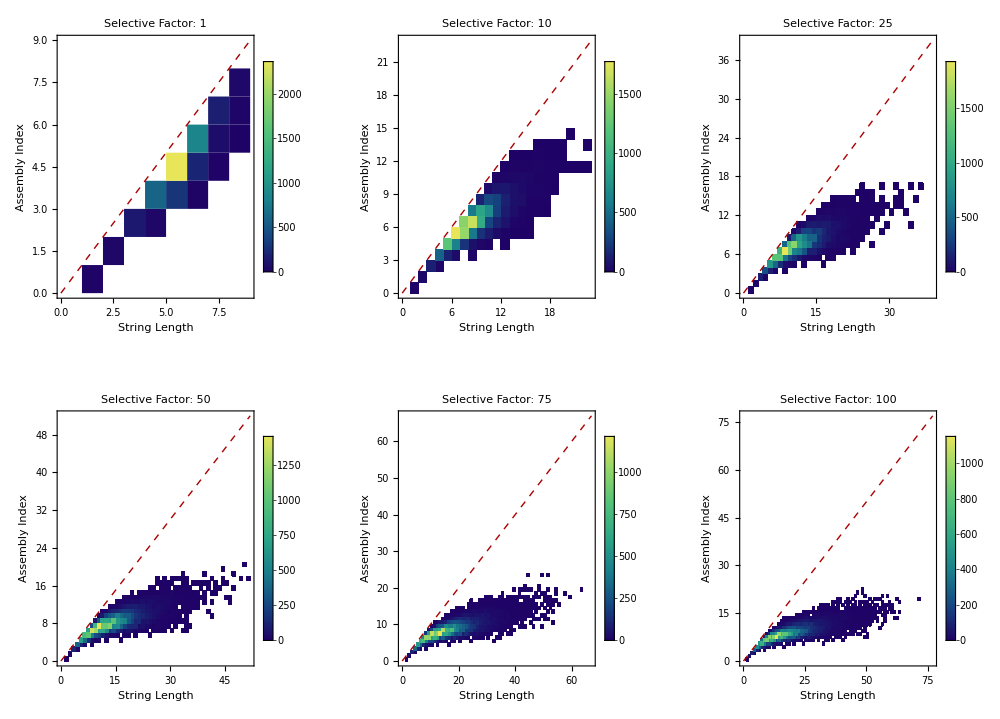

```mathematica
GraphicsGrid[Partition[outputPlots,3],ImageSize->1000]
```

```mathematica
(* Replotting with logarithmic scale *)
```

```mathematica
outputPlots=Table[Block[{simDir,fileData,assemblyData,allData,pts,maxLength,binCounts,maxCount,logMax,majorCounts,legendTicks,colourFunction,legend,plot},simDir=baseDirectory<>"PeptideSimData/"<>"SelectiveFac_"<>ToString[selectiveFactorList[[k]]];
assemblyData=Table[fileData=Partition[StringSplit[Import[simDir<>"/string_data_"<>ToString[runID]<>"/seqList_"<>ToString[runID]<>".txtOut"],"\n"],2];
Table[{First@StringSplit[fileData[[i,1]]," "],ToExpression@Last@StringSplit[fileData[[i,1]]," "]},{i,Length[fileData]}],{runID,nRuns}];
allData=Flatten[assemblyData,1];
pts={StringLength[#[[1]]],#[[2]]}&/@allData;
maxLength=Ceiling[Max[Flatten[pts]]]+1;
binCounts=BinCounts[pts,{0,maxLength,1},{0,maxLength,1}];
maxCount=Max[Flatten[binCounts]];
logMax=Log10[maxCount];
majorCounts=10^Range[0,Floor[Log10[maxCount]]];
legendTicks={Log10[#],NumberForm[#,DigitBlock->3]}&/@majorCounts;
colourFunction=Function[z,If[z<=0,Directive[White,Opacity[0]],ColorData["BlueGreenYellow"][Rescale[Log10[z],{0,logMax}]]]];
legend=BarLegend[{"BlueGreenYellow",{0,logMax}},Ticks->legendTicks,LegendMarkerSize->{10,180},LabelStyle->Directive[Black,FontSize->16]];
plot=DensityHistogram[pts,{{0,maxLength,1},{0,maxLength,1}},"Count",PlotLabel->"Selective Factor: "<>ToString[selectiveFactorList[[k]]],ColorFunction->colourFunction,ColorFunctionScaling->False,ChartLegends->Placed[legend,{Scaled[{0.06,0.94}],{0.2,0.95}}],AspectRatio->1,Frame->True,FrameLabel->{"String Length","Assembly Index"},LabelStyle->Directive[Black,FontSize->18],Epilog->{Darker@Red,Dashed,Line[{{0,0},{maxLength,maxLength}}]},PlotRange->{{0,maxLength},{0,maxLength}},ImageSize->300];
Export[simDir<>"/Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>"LogPlot.png",plot,ImageResolution->300];
Export[simDir<>"/Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>"LogPlot.svg",plot];
plot],{k,Length[selectiveFactorList]}];
```

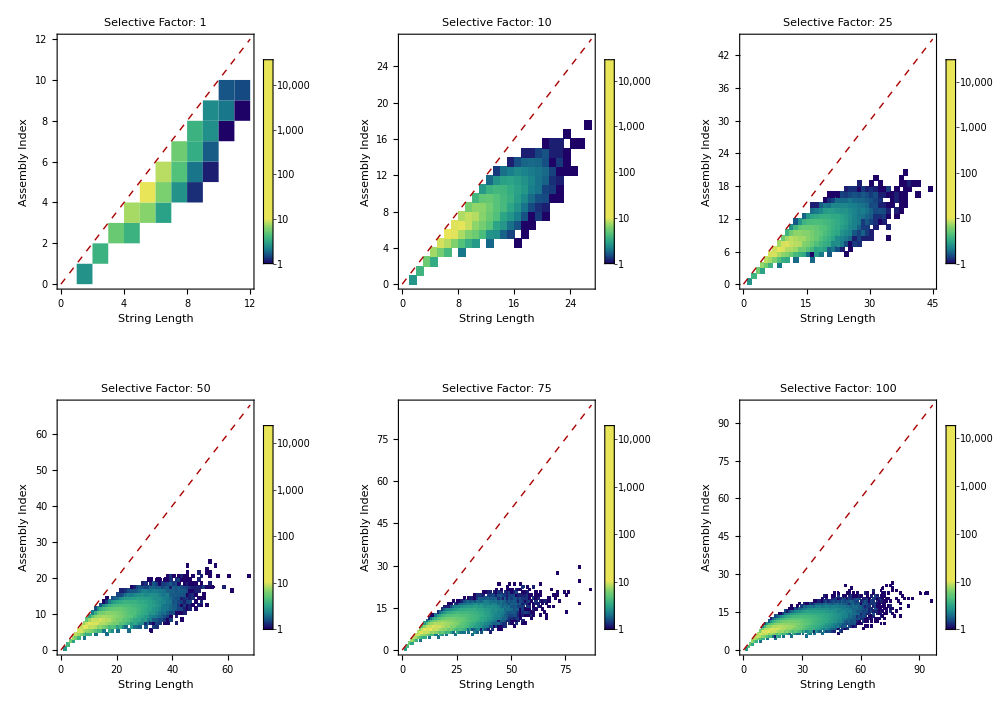

```mathematica
GraphicsGrid[Partition[outputPlots,3],ImageSize->1000]
```

```mathematica
outputPlots2=Table[dataList=Block[{simDir,assemblyData,dataList,dataListSorted,minmaxAssemblyIndex},simDir=baseDirectory<>"PeptideSimData/"<>"SelectiveFac_"<>ToString[selectiveFactorList[[k]]];
assemblyData=Table[fileData=Partition[StringSplit[Import[simDir<>"/string_data_"<>ToString[runID]<>"/seqList_"<>ToString[runID]<>".txtOut"],"\n"],2];
dataList=Table[{First@StringSplit[fileData[[i]][[1]]," "],ToExpression@Last@StringSplit[fileData[[i]][[1]]," "]},{i,Length@fileData}],{runID,nRuns}]];
dataListSorted=Monitor[Table[Block[{maxAssemblyIndex=Max@dataList[[runID]][[All,2]]},Table[Select[dataList[[runID]],#[[2]]==ai&],{ai,0,maxAssemblyIndex}]],{runID,nRuns}],runID];
minmaxAssemblyIndex=Min@Table[(First@Last@dataListSorted[[i]])[[2]],{i,Length@dataListSorted}];
plot=ListPlot[Table[Block[{pairData,simList},pairData=Subsets[Block[{data=dataListSorted[[All,j]]},data[[#]][[All,1]]&/@Range[nRuns]],{2}];
simList=Table[N@((Length@(Intersection@@pairData[[i]]))/(Length@(Union@@pairData[[i]]))),{i,Length@pairData}];Around[Mean@simList,StandardDeviation@simList]],{j,minmaxAssemblyIndex}],PlotLabel->"Selective Factor: "<>ToString[selectiveFactorList[[k]]],AspectRatio->1,Frame->True,FrameLabel->{"Assembly Index","Similarity"},PlotStyle->{Black,PointSize[0.02]},Filling->Axis,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},ImageSize->300];Export[baseDirectory<>"PeptideSimData/"<>"/Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>"_SimilarityPlot.png",plot,ImageResolution->300];

Export[baseDirectory<>"PeptideSimData/"<>"/Distribution_SF_"<>ToString[selectiveFactorList[[k]]]<>"_SimilarityPlot.svg",plot];plot,{k,Length@selectiveFactorList}];
```

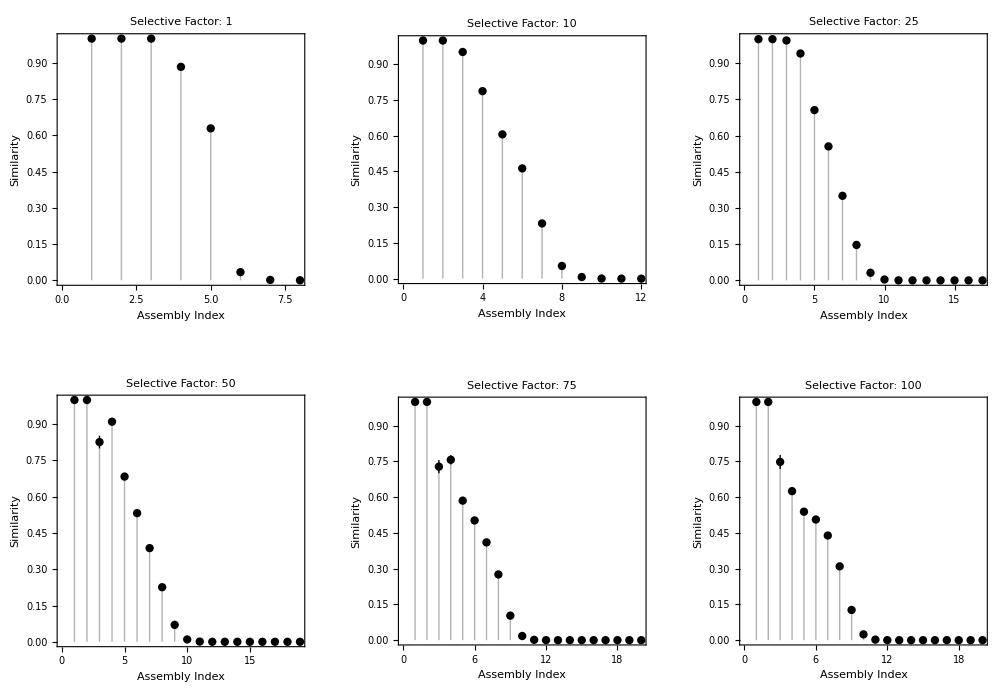

```mathematica
GraphicsGrid[Partition[outputPlots2,3],ImageSize->1000]
```

```mathematica
explorationData=Delete[Import[baseDirectory<>"PeptideSimData/jas_final.csv"],{1}];
```

```mathematica
dataF=Partition[explorationData[[All,8]],16];
```

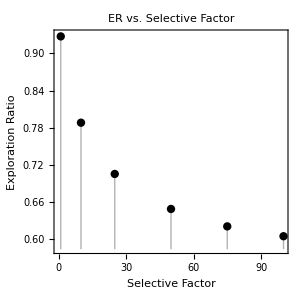

```mathematica
outputPlot3=ListPlot[Transpose@{selectiveFactorList,Around[Mean[#],StandardDeviation[#]]&/@dataF},PlotStyle->{Black,PointSize[0.02]},Frame->True,PlotLabel->"ER vs. Selective Factor",AspectRatio->1,FrameLabel->{"Selective Factor","Exploration Ratio"},Filling->Axis,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"ExplorationRatio_Sim.svg",outputPlot3]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/ExplorationRatio_Sim.svg

```mathematica
Export[baseDirectory<>"ExplorationRatio_Sim.png",outputPlot3,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/0_Completed/Peptide_Selection/Fig_3/ExplorationRatio_Sim.png